# Time-dependent TFD covariance matrix generation

```mathematica
Quit[]
```

```mathematica
ClearAll["Global`*"]
```

```mathematica
SetDirectory[NotebookDirectory[]];
<<GaussianOptimization`
```

## 1. Computationally efficient construction via FT and Toeplitz matrices

### Fundamental Definitions

```mathematica
k[NN_,l_,j_]:=2Pi j/(NN l);
```

```mathematica
ω[NN_,l_,m_,i_]:=√(m^2+(2/l Sin[(π i)/NN])^2); (* i enumerates the lattice sites *)
```

```mathematica
α[NN_,l_,m_,β_,ω_]:=1/2 Log[Coth[(β ω)/4]];
```

### Time-independent blocks (thermal states)

```mathematica
(* GTI stands for "Cov. matrix Time Independent" *)
GTI[NN_,l_,m_,β_]:=Module[{ωlist,αlist,ϕcorrs,πcorrs,params,blocks},

ωlist=Table[ω[NN,l,m,i]//N,{i,0,NN-1}];
αlist=Table[α[NN,l,m,β,ω],{ω,ωlist}];

params=Thread[{ωlist,αlist}];
ϕcorrs=Fourier[Table[Sqrt[1/NN] Cosh[2 param[[2]]]/param[[1]],{param,params}]]//Re;
πcorrs=Fourier[Table[Sqrt[1/NN] Cosh[2 param[[2]]] param[[1]],{param,params}]]//Re;

blocks=ToeplitzMatrix/@{ϕcorrs,πcorrs};
DiagonalMatrix[Hold/@blocks]//ReleaseHold//ArrayFlatten
];
```

### Time-dependent blocks (inter-system correlations)

```mathematica
(* GTD stands for "Cov. matrix Time Dependent" *)
GTD[t_,NN_,l_,m_,β_]:=GTD[t,NN,l,m,β]=Module[{ωlist,αlist,params,ϕπcorrs,ϕϕcorrs,ππcorrs,ϕπblock,ϕϕblock,ππblock},

ωlist=Table[ω[NN,l,m,i]//N,{i,0,NN-1}];
αlist=Table[α[NN,l,m,β,ω],{ω,ωlist}];

params=Thread[{ωlist,αlist}];
ϕϕcorrs=Fourier[Table[-Sqrt[1/NN] Cos[param[[1]] t] Sinh[2 param[[2]]]/param[[1]],{param,params}]]//Re;
ππcorrs=Fourier[Table[Sqrt[1/NN] Cos[param[[1]] t] Sinh[2 param[[2]] param[[1]]],{param,params}]]//Re;
ϕπcorrs=Fourier[Table[Sqrt[1/NN] Sin[param[[1]] t] Sinh[2 param[[2]]],{param,params}]]//Re;

{ϕϕblock,ππblock,ϕπblock}=ToeplitzMatrix/@{ϕϕcorrs,ππcorrs,ϕπcorrs};

ArrayFlatten[{{ϕϕblock,ϕπblock},{ϕπblock,ππblock}}]];
```

### Constructing the full covariance matrix

```mathematica
GTFDqqpp[{t_,NN_,l_,m_,β_}]:=Module[{TI,TD},
TI=GTI[NN,l,m,β];
TD=GTD[t,NN,l,m,β];
ArrayFlatten[{{TI,TD},{TD,TI}}]];

GTFDqpqp[{t_,NN_,l_,m_,β_}]:=Module[{Gqqpp,Mtra,MTra},
Gqqpp=GTFDqqpp[t,NN,l,m,β];
Mtra=GOqpqpFROMqqpp[Length[Gqqpp]/4];
MTra=DiagonalMatrix[Hold/@{Mtra,Mtra}]//ReleaseHold//ArrayFlatten;
MTra.Gqqpp.Transpose[MTra]
];
```

### Basic sanity checks

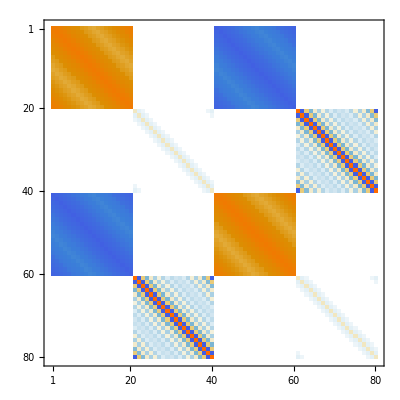

```mathematica
(* Basic matrix plots to compare with Lucas' notes *)
GTFDqqpp[{0,20,1,.05,.01}]//MatrixPlot
(* This doesn't look right at all *)
```

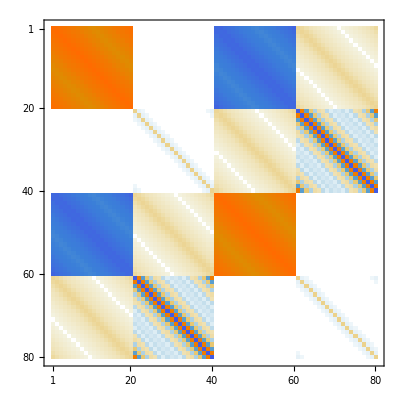

```mathematica
GTFDqqpp[{1.4,20,1,.05,.01}]//MatrixPlot
(* Time evolution seems to work correctly *)
```

## 2. Explicit construction

### Fundamental Definitions

```mathematica
k[NN_,l_,j_]:=2Pi j/(NN l);
```

```mathematica
ω[NN_,l_,m_,i_]:=√(m^2+(2/l Sin[(π i)/NN])^2);
```

```mathematica
α[NN_,l_,m_,β_,ω_]:=1/2 Log[Coth[(β ω)/4]];
```

### Time-independent blocks (thermal states)

-Graphics-

```mathematica
CovϕϕLL[x_,y_,NN_,l_,m_,β_]:=1/NN Sum[
Exp[I (x-y) k[NN,l,j]] Cosh[2 α[NN,l,m,β,ω[NN,l,m,j]]]/ω[NN,l,m,j]//N//Re
,{j,1,NN}];
```

```mathematica
CovππLL[x_,y_,NN_,l_,m_,β_]:=1/NN Sum[
Exp[I (x-y) k[NN,l,j]] Cosh[2 α[NN,l,m,β,ω[NN,l,m,j]]] ω[NN,l,m,j]//N//Re
,{j,1,NN}];
```

```mathematica
(* Thermal state CM in qqpp basis *)
CMThTI[NN_,l_,m_,β_]:=Module[{Gϕϕ,Gππ},
Gϕϕ=Table[CovϕϕLL[x,y,NN,l,m,β],{x,NN},{y,NN}];
Gππ=Table[CovππLL[x,y,NN,l,m,β],{x,NN},{y,NN}];
DiagonalMatrix[Hold/@{Gϕϕ,Gππ}]//ReleaseHold//ArrayFlatten];
```

### Time-dependent blocks (inter-system correlations)

-Graphics-

```mathematica
CovϕϕLR[t_,x_,y_,NN_,l_,m_,β_]:=-1/NN Sum[
Exp[I (x-y) k[NN,l,j]] Cos[ω[NN,l,m,j] t] Sinh[2 α[NN,l,m,β,ω[NN,l,m,j]]]/ω[NN,l,m,j]//N//Re
,{j,1,NN}];
```

```mathematica
CovππLR[t_,x_,y_,NN_,l_,m_,β_]:=1/NN Sum[
Exp[I (x-y) k[NN,l,j]] Cos[ω[NN,l,m,j] t] Sinh[2 α[NN,l,m,β,ω[NN,l,m,j]]] ω[NN,l,m,j]//N//Re
,{j,1,NN}];
```

```mathematica
CovϕπLR[t_,x_,y_,NN_,l_,m_,β_]:=-1/NN Sum[
Exp[I (x-y) k[NN,l,j]] Sin[ω[NN,l,m,j] t] Sinh[2 α[NN,l,m,β,ω[NN,l,m,j]]]//N//Re
,{j,1,NN}];
```

```mathematica
(* in qqpp basis *)
CMThTD[t_,NN_,l_,m_,β_]:=Module[{Gϕϕ,Gππ,Gϕπ},
Gϕϕ=Table[CovϕϕLR[t,x,y,NN,l,m,β],{x,NN},{y,NN}];
Gππ=Table[CovππLR[t,x,y,NN,l,m,β],{x,NN},{y,NN}];
Gϕπ=Table[CovϕπLR[t,x,y,NN,l,m,β],{x,NN},{y,NN}];
ArrayFlatten[{{Gϕϕ,Gϕπ},{Gϕπ,Gππ}}]];
```

### Constructing the full covariance matrix

```mathematica
CMTFDqqpp[{t_,NN_,l_,m_,β_}]:=Module[{TI,TD},
TI=CMThTI[NN,l,m,β];
TD=CMThTD[t,NN,l,m,β];
ArrayFlatten[{{TI,TD},{TD,TI}}]];

CMTFDqpqp[{t_,NN_,l_,m_,β_}]:=Module[{Gqqpp,Mtra,MTra},
Gqqpp=CMTFDqqpp[t,NN,l,m,β];
Mtra=GOqpqpFROMqqpp[Length[Gqqpp]/4];
MTra=DiagonalMatrix[Hold/@{Mtra,Mtra}]//ReleaseHold//ArrayFlatten;
MTra.Gqqpp.Transpose[MTra]
];
```

### Basic sanity checks

```mathematica
(* Basic matrix plots to compare with Lucas' notes *)
CMTFDqqpp[0,20,1,.05,.01]//MatrixPlot
(* This looks similar to the plot in the notes, difference might be because of the choice of the system parameters *)
```

MatrixPlot::mat0: Argument CMTFDqqpp[0,20,1,0.05,0.01] at position 1 is not a matrix.

MatrixPlot[CMTFDqqpp[0,20,1,0.05,0.01]]

```mathematica
CMTFDqqpp[1.4,20,1,.05,.01]//MatrixPlot
(* Time evolution seems to work correctly *)
```

MatrixPlot::mat0: Argument CMTFDqqpp[1.4,20,1,0.05,0.01] at position 1 is not a matrix.

MatrixPlot[CMTFDqqpp[1.4,20,1,0.05,0.01]]

## 3. Consistency check

Checks to see whether both implementations of the construction agree:

```mathematica
vars={1.4,20,1,1,.01};
```

```mathematica
GTFDqqpp[vars]==CMTFDqqpp[vars]
```

True